```mathematica
C20[a_, b_, c_, d_, e_]:=(a&&b)⊻(a&&c)⊻(a&&d)⊻(a&&e)⊻(b&&c)⊻(b&&d)⊻(b&&e)⊻(c&&d)⊻(c&&e)⊻(d&&e)⊻(a&&b&&c)⊻(a&&b&&d)⊻(a&&b&&e)⊻(a&&c&&d)⊻(a&&c&&e)⊻(a&&d&&e)⊻(b&&c&&d)⊻(b&&c&&e)⊻(b&&d&&e)⊻(c&&d&&e)⊻(a&&b&&c&&d)⊻(a&&b&&c&&e)⊻(a&&b&&d&&e)⊻(a&&c&&d&&e)⊻(b&&c&&d&&e)⊻(a&&b&&c&&d&&e)
```

```mathematica
R=FromDigits[Table[If[C20@@((#==1)&/@IntegerDigits[i, 2, 5]), 1, 0], {i, 0, 31}]//Reverse, 2]
```

1771476584

```mathematica
is={151,187,189,195,635,27695,86371,125231,127647,204771,339567,350037,391075,595703,610999,618647,678175,695711,706101,774295,774333,815595,819183,954519,954559,1237143,1237183,1237267,1330799,1364159,1412395,1548439,1548477,1548479,1587939,1598843,1617823,1642687,1742015,1747775,1782335,1910319,2018927,2403611,2474175,2526507,2728127,2728211,2729627,2776223,2780371,3241823,3276771,3567003,4892427,5088227,5385595,5399333,5405669,5432979,5536055,5564707,5602651,6065451,6433339,6553571,6874491,9465019,9784943,10404475,10598971,10786397,10895547,10911935,10916027,10944199,11127715,11201851,11204955,11303891,11329055,12228447,12386493,12527263,12535715,12696663,12849875,13049531,13107171,13266631,14525883,14579503,14586159,14871103,16044639,18926267,18976043,19172987,19222331,19245467,19302907,19319587,19439003,21807957,21831867,22160683,22209835,22239935,22376403,22380383,22588411,24456815,24773403,25577087,25891003,26184527,26411803,26653483,27618715,27633819,27925755,28864891,29184367,29333687,31799455,32938687,38399331,39183739,43437205,43582219,43592251,43663547,44495867,45582051,45723659,48795867,48812219,51023451,51285727,51640227,51745291,51781819,51885803,52059027,52398051,52398059,52687695,52826835,54955307,54990715,56963639,57282839,57454543,57938199,58516399,76006115,76897975,77453987,78018539,83231355,85004475,85242515,85274779,85946687,87329275,88421059,88450019,88620757,88808315,89009171,89713351,90551695,90618735,96789883,97848603,97854819,103172247,104653627,105874155,108706975,109449495,113387255,114409915,116484695,156455931,161328251,162711195,166462075,170008923,171894139,174507947,177611119,177919387,177923887,178229667,179225243,180791867,182665195,194174363,196539947,207144799,209117819,212919675,219990367,222709467,230850383,233729423,256296063,265113855,303329851,306664815,307705335,326551467,339196707,342942891,351191707,351351957,353609107,354852283,355149603,355221725,355233067,355836899,356440885,357900923,358098659,358217635,359265019,366548907,390392403,392401907,412128035,439966971,446040343,449013151,461498927,462873211,515615551,615854955,624251727,624263295,624670559,626231967,626618539,650791727,652371995,681615983,682706851,683316117,686543765,689521275,689568415,689644255,691132255,693725755,695265523,698853085,700367455,702928607,706340731,709697903,709704011,711221045,711667867,714335699,722832181,724693391,731224763,734159407,746177147,747947675,768122299,781045535,824853115,830661975,833361835,833738539,834420063,853096691,854240879,879660155,895008475,895915067,895919707,902828731,904435551,905659003,913155359,914299131,915155515,916317527,924129019,924132151,924280187,932233679,932817119,933106939,933880827,938075479,1033662015,1033711215,1228187403,1268339499,1293576619,1356023211,1356813795,1366567315,1373334187,1380563003,1391143995,1395105059,1398177391,1400857979,1415102739,1419397819,1424279203,1425541395,1429562527,1432264303,1445083695,1446293439,1452976319,1466870331,1545889427,1549607459,1557735995,1566516639,1632981887,1638070251,1646590299,1647094127,1649094255,1649634863,1660153367,1660282703,1660407999,1668556639,1670333923,1675242043,1675813599,1675830483,1676043947,1677593679,1680050943,1690863771,1691213051,1694420123,1700054651,1705850783,1739183483,1752346223,1783769311,1783774295,1784201979,1791229115,1847223547,1864417967,1865282303,1970963375,2038253695,2429283903,2432196603,2439999639,2453026975,2456374895,2457432515,2467720331,2473479835,2488950619,2495587243,2497093023,2497124491,2497149615,2498689327,2502652055,2504930655,2507383339,2533978263,2544824075,2562023743,2695337307,2724296931,2724887967,2725424751,2746835787,2749681815,2749681855,2759500451,2764461691,2773151295,2775883163,2780736623,2781733055,2781733139,2793797539,2812620399,2817194331,2828399395,2830205231,2830217047,2862014815,2868487835,2870308031,2890290943,2892584739,2895981115,2897400437,2917377555,3092444963,3105515947,3106508075,3109198507,3131718331,3171512471,3171518447,3171525919,3171548243,3171668119,3175930527,3178590955,3207188671,3207609695,3252099323,3263853267,3268588375,3276342571,3285672599,3286195887,3294193419,3302628235,3304487259,3304767395,3304893499,3309644187,3312499871,3319437995,3320313515,3320815807,3343654855,3352276907,3354958767,3355027211,3355315279,3377445899,3393163415,3411161903,3413024155,3480334063,3504663167,3505459595,3516511039,3561344623,3567557291,3567749551,3568375327,3577015291,3580838747,3583394903,3617259199,3649717335,3652614491,3652637359,3659176879,3667891031,3674600695,3898720831,3909709975,3909715951,3909865623,3978243695,4016607423,4092975663,4134710895,4152033983,4170861119,4176975775,4245409983};
```

```mathematica
Table[Labeled[ArrayPlot[CellularAutomaton[{R, 2, 2}, {IntegerDigits[i, 2], 0}, 100], ImageSize->Small], i], {i, is}]
```

{-Graphics-151,-Graphics-187,-Graphics-189,-Graphics-195,-Graphics-635,-Graphics-27695,-Graphics-86371,-Graphics-125231,-Graphics-127647,-Graphics-204771,-Graphics-339567,-Graphics-350037,-Graphics-391075,-Graphics-595703,-Graphics-610999,-Graphics-618647,-Graphics-678175,-Graphics-695711,-Graphics-706101,-Graphics-774295,-Graphics-774333,-Graphics-815595,-Graphics-819183,-Graphics-954519,-Graphics-954559,-Graphics-1237143,-Graphics-1237183,-Graphics-1237267,-Graphics-1330799,-Graphics-1364159,-Graphics-1412395,-Graphics-1548439,-Graphics-1548477,-Graphics-1548479,-Graphics-1587939,-Graphics-1598843,-Graphics-1617823,-Graphics-1642687,-Graphics-1742015,-Graphics-1747775,-Graphics-1782335,-Graphics-1910319,-Graphics-2018927,-Graphics-2403611,-Graphics-2474175,-Graphics-2526507,-Graphics-2728127,-Graphics-2728211,-Graphics-2729627,-Graphics-2776223,-Graphics-2780371,-Graphics-3241823,-Graphics-3276771,-Graphics-3567003,-Graphics-4892427,-Graphics-5088227,-Graphics-5385595,-Graphics-5399333,-Graphics-5405669,-Graphics-5432979,-Graphics-5536055,-Graphics-5564707,-Graphics-5602651,-Graphics-6065451,-Graphics-6433339,-Graphics-6553571,-Graphics-6874491,-Graphics-9465019,-Graphics-9784943,-Graphics-10404475,-Graphics-10598971,-Graphics-10786397,-Graphics-10895547,-Graphics-10911935,-Graphics-10916027,-Graphics-10944199,-Graphics-11127715,-Graphics-11201851,-Graphics-11204955,-Graphics-11303891,-Graphics-11329055,-Graphics-12228447,-Graphics-12386493,-Graphics-12527263,-Graphics-12535715,-Graphics-12696663,-Graphics-12849875,-Graphics-13049531,-Graphics-13107171,-Graphics-13266631,-Graphics-14525883,-Graphics-14579503,-Graphics-14586159,-Graphics-14871103,-Graphics-16044639,-Graphics-18926267,-Graphics-18976043,-Graphics-19172987,-Graphics-19222331,-Graphics-19245467,-Graphics-19302907,-Graphics-19319587,-Graphics-19439003,-Graphics-21807957,-Graphics-21831867,-Graphics-22160683,-Graphics-22209835,-Graphics-22239935,-Graphics-22376403,-Graphics-22380383,-Graphics-22588411,-Graphics-24456815,-Graphics-24773403,-Graphics-25577087,-Graphics-25891003,-Graphics-26184527,-Graphics-26411803,-Graphics-26653483,-Graphics-27618715,-Graphics-27633819,-Graphics-27925755,-Graphics-28864891,-Graphics-29184367,-Graphics-29333687,-Graphics-31799455,-Graphics-32938687,-Graphics-38399331,-Graphics-39183739,-Graphics-43437205,-Graphics-43582219,-Graphics-43592251,-Graphics-43663547,-Graphics-44495867,-Graphics-45582051,-Graphics-45723659,-Graphics-48795867,-Graphics-48812219,-Graphics-51023451,-Graphics-51285727,-Graphics-51640227,-Graphics-51745291,-Graphics-51781819,-Graphics-51885803,-Graphics-52059027,-Graphics-52398051,-Graphics-52398059,-Graphics-52687695,-Graphics-52826835,-Graphics-54955307,-Graphics-54990715,-Graphics-56963639,-Graphics-57282839,-Graphics-57454543,-Graphics-57938199,-Graphics-58516399,-Graphics-76006115,-Graphics-76897975,-Graphics-77453987,-Graphics-78018539,-Graphics-83231355,-Graphics-85004475,-Graphics-85242515,-Graphics-85274779,-Graphics-85946687,-Graphics-87329275,-Graphics-88421059,-Graphics-88450019,-Graphics-88620757,-Graphics-88808315,-Graphics-89009171,-Graphics-89713351,-Graphics-90551695,-Graphics-90618735,-Graphics-96789883,-Graphics-97848603,-Graphics-97854819,-Graphics-103172247,-Graphics-104653627,-Graphics-105874155,-Graphics-108706975,-Graphics-109449495,-Graphics-113387255,-Graphics-114409915,-Graphics-116484695,-Graphics-156455931,-Graphics-161328251,-Graphics-162711195,-Graphics-166462075,-Graphics-170008923,-Graphics-171894139,-Graphics-174507947,-Graphics-177611119,-Graphics-177919387,-Graphics-177923887,-Graphics-178229667,-Graphics-179225243,-Graphics-180791867,-Graphics-182665195,-Graphics-194174363,-Graphics-196539947,-Graphics-207144799,-Graphics-209117819,-Graphics-212919675,-Graphics-219990367,-Graphics-222709467,-Graphics-230850383,-Graphics-233729423,-Graphics-256296063,-Graphics-265113855,-Graphics-303329851,-Graphics-306664815,-Graphics-307705335,-Graphics-326551467,-Graphics-339196707,-Graphics-342942891,-Graphics-351191707,-Graphics-351351957,-Graphics-353609107,-Graphics-354852283,-Graphics-355149603,-Graphics-355221725,-Graphics-355233067,-Graphics-355836899,-Graphics-356440885,-Graphics-357900923,-Graphics-358098659,-Graphics-358217635,-Graphics-359265019,-Graphics-366548907,-Graphics-390392403,-Graphics-392401907,-Graphics-412128035,-Graphics-439966971,-Graphics-446040343,-Graphics-449013151,-Graphics-461498927,-Graphics-462873211,-Graphics-515615551,-Graphics-615854955,-Graphics-624251727,-Graphics-624263295,-Graphics-624670559,-Graphics-626231967,-Graphics-626618539,-Graphics-650791727,-Graphics-652371995,-Graphics-681615983,-Graphics-682706851,-Graphics-683316117,-Graphics-686543765,-Graphics-689521275,-Graphics-689568415,-Graphics-689644255,-Graphics-691132255,-Graphics-693725755,-Graphics-695265523,-Graphics-698853085,-Graphics-700367455,-Graphics-702928607,-Graphics-706340731,-Graphics-709697903,-Graphics-709704011,-Graphics-711221045,-Graphics-711667867,-Graphics-714335699,-Graphics-722832181,-Graphics-724693391,-Graphics-731224763,-Graphics-734159407,-Graphics-746177147,-Graphics-747947675,-Graphics-768122299,-Graphics-781045535,-Graphics-824853115,-Graphics-830661975,-Graphics-833361835,-Graphics-833738539,-Graphics-834420063,-Graphics-853096691,-Graphics-854240879,-Graphics-879660155,-Graphics-895008475,-Graphics-895915067,-Graphics-895919707,-Graphics-902828731,-Graphics-904435551,-Graphics-905659003,-Graphics-913155359,-Graphics-914299131,-Graphics-915155515,-Graphics-916317527,-Graphics-924129019,-Graphics-924132151,-Graphics-924280187,-Graphics-932233679,-Graphics-932817119,-Graphics-933106939,-Graphics-933880827,-Graphics-938075479,-Graphics-1033662015,-Graphics-1033711215,-Graphics-1228187403,-Graphics-1268339499,-Graphics-1293576619,-Graphics-1356023211,-Graphics-1356813795,-Graphics-1366567315,-Graphics-1373334187,-Graphics-1380563003,-Graphics-1391143995,-Graphics-1395105059,-Graphics-1398177391,-Graphics-1400857979,-Graphics-1415102739,-Graphics-1419397819,-Graphics-1424279203,-Graphics-1425541395,-Graphics-1429562527,-Graphics-1432264303,-Graphics-1445083695,-Graphics-1446293439,-Graphics-1452976319,-Graphics-1466870331,-Graphics-1545889427,-Graphics-1549607459,-Graphics-1557735995,-Graphics-1566516639,-Graphics-1632981887,-Graphics-1638070251,-Graphics-1646590299,-Graphics-1647094127,-Graphics-1649094255,-Graphics-1649634863,-Graphics-1660153367,-Graphics-1660282703,-Graphics-1660407999,-Graphics-1668556639,-Graphics-1670333923,-Graphics-1675242043,-Graphics-1675813599,-Graphics-1675830483,-Graphics-1676043947,-Graphics-1677593679,-Graphics-1680050943,-Graphics-1690863771,-Graphics-1691213051,-Graphics-1694420123,-Graphics-1700054651,-Graphics-1705850783,-Graphics-1739183483,-Graphics-1752346223,-Graphics-1783769311,-Graphics-1783774295,-Graphics-1784201979,-Graphics-1791229115,-Graphics-1847223547,-Graphics-1864417967,-Graphics-1865282303,-Graphics-1970963375,-Graphics-2038253695,-Graphics-2429283903,-Graphics-2432196603,-Graphics-2439999639,-Graphics-2453026975,-Graphics-2456374895,-Graphics-2457432515,-Graphics-2467720331,-Graphics-2473479835,-Graphics-2488950619,-Graphics-2495587243,-Graphics-2497093023,-Graphics-2497124491,-Graphics-2497149615,-Graphics-2498689327,-Graphics-2502652055,-Graphics-2504930655,-Graphics-2507383339,-Graphics-2533978263,-Graphics-2544824075,-Graphics-2562023743,-Graphics-2695337307,-Graphics-2724296931,-Graphics-2724887967,-Graphics-2725424751,-Graphics-2746835787,-Graphics-2749681815,-Graphics-2749681855,-Graphics-2759500451,-Graphics-2764461691,-Graphics-2773151295,-Graphics-2775883163,-Graphics-2780736623,-Graphics-2781733055,-Graphics-2781733139,-Graphics-2793797539,-Graphics-2812620399,-Graphics-2817194331,-Graphics-2828399395,-Graphics-2830205231,-Graphics-2830217047,-Graphics-2862014815,-Graphics-2868487835,-Graphics-2870308031,-Graphics-2890290943,-Graphics-2892584739,-Graphics-2895981115,-Graphics-2897400437,-Graphics-2917377555,-Graphics-3092444963,-Graphics-3105515947,-Graphics-3106508075,-Graphics-3109198507,-Graphics-3131718331,-Graphics-3171512471,-Graphics-3171518447,-Graphics-3171525919,-Graphics-3171548243,-Graphics-3171668119,-Graphics-3175930527,-Graphics-3178590955,-Graphics-3207188671,-Graphics-3207609695,-Graphics-3252099323,-Graphics-3263853267,-Graphics-3268588375,-Graphics-3276342571,-Graphics-3285672599,-Graphics-3286195887,-Graphics-3294193419,-Graphics-3302628235,-Graphics-3304487259,-Graphics-3304767395,-Graphics-3304893499,-Graphics-3309644187,-Graphics-3312499871,-Graphics-3319437995,-Graphics-3320313515,-Graphics-3320815807,-Graphics-3343654855,-Graphics-3352276907,-Graphics-3354958767,-Graphics-3355027211,-Graphics-3355315279,-Graphics-3377445899,-Graphics-3393163415,-Graphics-3411161903,-Graphics-3413024155,-Graphics-3480334063,-Graphics-3504663167,-Graphics-3505459595,-Graphics-3516511039,-Graphics-3561344623,-Graphics-3567557291,-Graphics-3567749551,-Graphics-3568375327,-Graphics-3577015291,-Graphics-3580838747,-Graphics-3583394903,-Graphics-3617259199,-Graphics-3649717335,-Graphics-3652614491,-Graphics-3652637359,-Graphics-3659176879,-Graphics-3667891031,-Graphics-3674600695,-Graphics-3898720831,-Graphics-3909709975,-Graphics-3909715951,-Graphics-3909865623,-Graphics-3978243695,-Graphics-4016607423,-Graphics-4092975663,-Graphics-4134710895,-Graphics-4152033983,-Graphics-4170861119,-Graphics-4176975775,-Graphics-4245409983}

```mathematica
is2={151,187,189,195,635,125231,595703,610999,1598843,5088227,14871103,256296063};
```

```mathematica
Table[Labeled[ArrayPlot[CellularAutomaton[{R, 2, 2}, {IntegerDigits[i, 2], 0}, 100], ImageSize->Small], i], {i, is2}]
```

{-Graphics-151,-Graphics-187,-Graphics-189,-Graphics-195,-Graphics-635,-Graphics-125231,-Graphics-595703,-Graphics-610999,-Graphics-1598843,-Graphics-5088227,-Graphics-14871103,-Graphics-256296063}

```mathematica
2^64
```

18446744073709551616

```mathematica
C21[a_, b_, c_, d_, e_]:=(a||b||c||d||e)⊻(a⊻b⊻c⊻d⊻e)
```

```mathematica
H=Table[C21@@(#==1&/@IntegerDigits[i, 2, 5]), {i, 0, 31}]
```

{False,False,False,True,False,True,True,False,False,True,True,False,True,False,False,True,False,True,True,False,True,False,False,True,True,False,False,True,False,True,True,False}

```mathematica
C22[a_, b_, c_, d_, e_]:=(a&&b)⊻(a&&c)⊻(a&&d)⊻(a&&e)⊻(b&&c)⊻(b&&d)⊻(b&&e)⊻(c&&d)⊻(c&&e)⊻(d&&e)⊻(a&&b&&c)⊻(a&&b&&d)⊻(a&&b&&e)⊻(a&&c&&d)⊻(a&&c&&e)⊻(a&&d&&e)⊻(b&&c&&d)⊻(b&&c&&e)⊻(b&&d&&e)⊻(c&&d&&e)⊻(a&&b&&c&&d)⊻(a&&b&&c&&e)⊻(a&&b&&d&&e)⊻(a&&c&&d&&e)⊻(b&&c&&d&&e)⊻(a&&b&&c&&d&&e)
```

```mathematica
K=Table[C22@@(#==1&/@IntegerDigits[i, 2, 5]), {i, 0, 31}]
```

{False,False,False,True,False,True,True,False,False,True,True,False,True,False,False,True,False,True,True,False,True,False,False,True,True,False,False,True,False,True,True,False}

```mathematica
H==K
```

True

```mathematica
Length[is]
```

477

```mathematica
uniquePatterns={151,187,189,195,635,125231,595703,610999,14871103,256296063};
Table[Labeled[ArrayPlot[CellularAutomaton[{1771476584, 2, 2}, {IntegerDigits[i, 2], 0}, 100], ImageSize->Small], i], {i, uniquePatterns}]
```

{-Graphics-151,-Graphics-187,-Graphics-189,-Graphics-195,-Graphics-635,-Graphics-125231,-Graphics-595703,-Graphics-610999,-Graphics-14871103,-Graphics-256296063}

```mathematica
ps=ResourceData["Persistent Structures in the Code 20 Cellular Automaton"]
dl=ps[All, "Number"]//Normal
existingResults=dl;
```

{151,187,189,195,221,635,889,125231,595703,610999,14871103,16537415,256296063,22503642597,222678959859,10495070598767,360759087837221,2197520782601119,11221488970893447375,142082121178470981231}

{151,187,189,195,221,635,889,125231,595703,610999,14871103,16537415,256296063,22503642597,222678959859,10495070598767,360759087837221,2197520782601119,11221488970893447375,142082121178470981231}

```mathematica
{151,187,189,195,221,635,889,125231,595703,610999,14871103,16537415,256296063,22503642597,222678959859,10495070598767,360759087837221,2197520782601119,11221488970893447375,142082121178470981231};
```

```mathematica
Table[Labeled[ArrayPlot[CellularAutomaton[{1771476584, 2, 2}, {IntegerDigits[i, 2], 0}, 100], ImageSize->Small], i], {i, dl}]
```

{-Graphics-151,-Graphics-187,-Graphics-189,-Graphics-195,-Graphics-221,-Graphics-635,-Graphics-889,-Graphics-125231,-Graphics-595703,-Graphics-610999,-Graphics-14871103,-Graphics-16537415,-Graphics-256296063,-Graphics-22503642597,-Graphics-222678959859,-Graphics-10495070598767,-Graphics-360759087837221,-Graphics-2197520782601119,-Graphics-11221488970893447375,-Graphics-142082121178470981231}

```mathematica
{151,187,189,195,221,635,889,125231,595703,610999,14871103,16537415,256296063,22503642597,222678959859,10495070598767}
Table[StringReplace[StringTrim@StringReplace[StringJoin[ToString/@Last[CellularAutomaton[{1771476584, 2, 2}, {IntegerDigits[i, 2], 0}, 100]]], "0"->" "], " "->"0"], {i, %}]//InputForm
```

{151,187,189,195,221,635,889,125231,595703,610999,14871103,16537415,256296063,22503642597,222678959859,10495070598767}

{"10010111", "101011011", "10111101", "1000010011111001111100100001", "110110101", "1001111011", "1101111001", "11101101110011111001110110111", "10010001011011110111", 
 "10010101001010110111", "111000101110101000111111", "111111000101011101000111", "1011000000011011111111101100000001101", "10100111101010100100101010111100101", 
 "1110001111011101001001001011101111000111", "10100110001011110110111100011001100100001101"}

```mathematica
Length[IntegerDigits[142082121178470981231, 2]]
```

67

```mathematica
IntegerDigits[42, 2]//Length
```

6

```mathematica
Floor[1+Log2[42]]//N
```

6.

```mathematica
is3={189,195,125231,353719573,222678959859,2858216684133,3602563616139,3752500737627,1882709341403,4354853977791,22525392922565,45447128787621,22860807121509,23084236910565,47825481056181,27796794113107,57476239530123,63960135103767,66572529830991,67447006132911,90615524371237,111187174489171,114246837472243,238853599673499,119788016052123,119903908091995,240350971599195,720812550858693,360406275794885,363482486100645,728912909450661,365501509250149,738695581642725,747179751360405,379533221882165,765207694491573,384261926403445,437389422716771,886197030157971,889497391332435,919045015531275,474121397819883,1426229341004869,2883250201241541,1516757620553269,3046951803112629,3460817532067107,3462532297542435,1846437220865931,3736551909467691,1870600381764907,1914305755055515,3828671135499675,1921073947436635,4337472437842287,4411175533083999,4414906557968223,6061634972553781,6072780964665653,6095549651451061,6994100551357283,7514584473913771,7673850042603611,15368591586715227,8674944877687151,46379094192005925,24054020750464853,48492467206873653,24291123848714549,24507282054071413,27943598967796067,56591250820608147,60845857397756955,70183802279029407,92813799444937509,192455392017708885,194328990766504245,222810305326786467,112135340176477411,116620516835136755,234921616604095755,119665541574658347,119673357152332075,239346820152863019,244692654671342235,122948732700943963,124217838421271867,276813948516055983,282315234292596063,758391531345913365,384788306081777493,769739333949806421,444349576867818147,900211856503261155,488481463471683355,489800984356700571,992293053755206203,496191305447529019,500405598360280187,1002891794279822715,503611058843264507,1136402098303216191,1492471093509311909,1524154636597521557,1530150601101313941,3075471559992319317,1555568624026504501,3829547428900809003,1957376017637044891,3920589980924593563,3938019990607059291,1995575197491900859,4015182254968194939,5959051569895417509,6096077823607098517,12196291990378742421,6098249687680500373,12423847549607761461,6226585985274170165,14165103659069810979,7083637998841116963,14172346966810457379,7171659533715878115,15363804635866131627,15373015871416429227,15404293086273135531,15662999107728079515,8803276207980341807};
Table[Labeled[ArrayPlot[CellularAutomaton[{1771476584, 2, 2}, {IntegerDigits[i, 2], 0}, 100], ImageSize->Small], i], {i, is3}]
```

{-Graphics-189,-Graphics-195,-Graphics-125231,-Graphics-353719573,-Graphics-222678959859,-Graphics-2858216684133,-Graphics-3602563616139,-Graphics-3752500737627,-Graphics-1882709341403,-Graphics-4354853977791,-Graphics-22525392922565,-Graphics-45447128787621,-Graphics-22860807121509,-Graphics-23084236910565,-Graphics-47825481056181,-Graphics-27796794113107,-Graphics-57476239530123,-Graphics-63960135103767,-Graphics-66572529830991,-Graphics-67447006132911,-Graphics-90615524371237,-Graphics-111187174489171,-Graphics-114246837472243,-Graphics-238853599673499,-Graphics-119788016052123,-Graphics-119903908091995,-Graphics-240350971599195,-Graphics-720812550858693,-Graphics-360406275794885,-Graphics-363482486100645,-Graphics-728912909450661,-Graphics-365501509250149,-Graphics-738695581642725,-Graphics-747179751360405,-Graphics-379533221882165,-Graphics-765207694491573,-Graphics-384261926403445,-Graphics-437389422716771,-Graphics-886197030157971,-Graphics-889497391332435,-Graphics-919045015531275,-Graphics-474121397819883,-Graphics-1426229341004869,-Graphics-2883250201241541,-Graphics-1516757620553269,-Graphics-3046951803112629,-Graphics-3460817532067107,-Graphics-3462532297542435,-Graphics-1846437220865931,-Graphics-3736551909467691,-Graphics-1870600381764907,-Graphics-1914305755055515,-Graphics-3828671135499675,-Graphics-1921073947436635,-Graphics-4337472437842287,-Graphics-4411175533083999,-Graphics-4414906557968223,-Graphics-6061634972553781,-Graphics-6072780964665653,-Graphics-6095549651451061,-Graphics-6994100551357283,-Graphics-7514584473913771,-Graphics-7673850042603611,-Graphics-15368591586715227,-Graphics-8674944877687151,-Graphics-46379094192005925,-Graphics-24054020750464853,-Graphics-48492467206873653,-Graphics-24291123848714549,-Graphics-24507282054071413,-Graphics-27943598967796067,-Graphics-56591250820608147,-Graphics-60845857397756955,-Graphics-70183802279029407,-Graphics-92813799444937509,-Graphics-192455392017708885,-Graphics-194328990766504245,-Graphics-222810305326786467,-Graphics-112135340176477411,-Graphics-116620516835136755,-Graphics-234921616604095755,-Graphics-119665541574658347,-Graphics-119673357152332075,-Graphics-239346820152863019,-Graphics-244692654671342235,-Graphics-122948732700943963,-Graphics-124217838421271867,-Graphics-276813948516055983,-Graphics-282315234292596063,-Graphics-758391531345913365,-Graphics-384788306081777493,-Graphics-769739333949806421,-Graphics-444349576867818147,-Graphics-900211856503261155,-Graphics-488481463471683355,-Graphics-489800984356700571,-Graphics-992293053755206203,-Graphics-496191305447529019,-Graphics-500405598360280187,-Graphics-1002891794279822715,-Graphics-503611058843264507,-Graphics-1136402098303216191,-Graphics-1492471093509311909,-Graphics-1524154636597521557,-Graphics-1530150601101313941,-Graphics-3075471559992319317,-Graphics-1555568624026504501,-Graphics-3829547428900809003,-Graphics-1957376017637044891,-Graphics-3920589980924593563,-Graphics-3938019990607059291,-Graphics-1995575197491900859,-Graphics-4015182254968194939,-Graphics-5959051569895417509,-Graphics-6096077823607098517,-Graphics-12196291990378742421,-Graphics-6098249687680500373,-Graphics-12423847549607761461,-Graphics-6226585985274170165,-Graphics-14165103659069810979,-Graphics-7083637998841116963,-Graphics-14172346966810457379,-Graphics-7171659533715878115,-Graphics-15363804635866131627,-Graphics-15373015871416429227,-Graphics-15404293086273135531,-Graphics-15662999107728079515,-Graphics-8803276207980341807}

```mathematica
488601000000000000
222678959859
90615524371237
```

488601000000000000

222678959859

90615524371237

```mathematica
IntegerDigits[222678959859, 2]
```

{1,1,0,0,1,1,1,1,0,1,1,0,0,0,1,0,1,1,0,0,1,1,0,1,0,0,0,1,1,0,1,1,1,1,0,0,1,1}

```mathematica
n={0,1,1,0,1,0,0,0,1,1,0,1,1,1,1,0,0,1,1}
```

{0,1,1,0,1,0,0,0,1,1,0,1,1,1,1,0,0,1,1}

```mathematica
Join[Reverse[n], n]
```

{1,1,0,0,1,1,1,1,0,1,1,0,0,0,1,0,1,1,0,0,1,1,0,1,0,0,0,1,1,0,1,1,1,1,0,0,1,1}

```mathematica
%==IntegerDigits[222678959859, 2]
```

True

```mathematica
FromDigits[n, 2]
```

214771

```mathematica
FromDigits[Reverse[n], 2]
```

424726

```mathematica
IntegerDigits[212363, 2]
```

{1,1,0,0,1,1,1,1,0,1,1,0,0,0,1,0,1,1}

```mathematica
NOVELSOLUTIONS={90615524371237};
Table[Labeled[ArrayPlot[CellularAutomaton[{1771476584, 2, 2}, {IntegerDigits[i, 2], 0}, 100], ImageSize->Medium], i], {i, NOVELSOLUTIONS}]
```

{-Graphics-90615524371237}

```mathematica
Table[Labeled[ArrayPlot[CellularAutomaton[{1771476584, 2, 2}, {IntegerDigits[i, 2], 0}, 100], ImageSize->Small], i], {i, {66355061549583000375358048449194801233920}}]
```

{-Graphics-66355061549583000375358048449194801233920}

```mathematica
CAP[l_]:=Table[Labeled[ArrayPlot[CellularAutomaton[{1771476584, 2, 2}, {IntegerDigits[i, 2], 0}, 100], ImageSize->Small], i], {i, l}]
```

```mathematica
CAP[dl]
```

{-Graphics-151,-Graphics-187,-Graphics-189,-Graphics-195,-Graphics-221,-Graphics-635,-Graphics-889,-Graphics-125231,-Graphics-595703,-Graphics-610999,-Graphics-14871103,-Graphics-16537415,-Graphics-256296063,-Graphics-22503642597,-Graphics-222678959859,-Graphics-10495070598767,-Graphics-360759087837221,-Graphics-2197520782601119,-Graphics-11221488970893447375,-Graphics-142082121178470981231}

```mathematica
CAP[{1882709341403,90615524371237}]
```

{-Graphics-1882709341403,-Graphics-90615524371237}

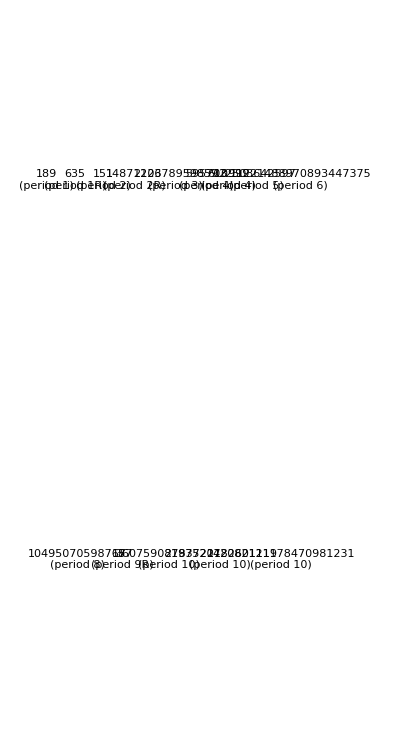

```mathematica
GraphicsColumn[{GraphicsRow[Labeled[RulePlot[CellularAutomaton[{20,{2,1},2}],CenterArray[IntegerDigits[#[[1]],2],400],200,PlotRange->{Automatic,#[[2]]},ImageSize->{Automatic,300}],Text[Style[ToString[#[[1]]]<>"\n"<>#[[3]],Italic,TextAlignment->Center]],ImageSize->{Automatic,330}]&/@{{189,{185,215},"(period 1)"},{635,{190,240},"(period 1R)"},{151,{185,215},"(period 2)"},{14871103,{180,240},"(period 2R)"},{222678959859,{170,230},"(period 3)"},{595703,{185,215},"(period 4)"},{610999,{185,215},"(period 4)"},{22503642597,{175,225},"(period 5)"},{11221488970893447375,{160,240},"(period 6)"}},ImageSize->{Automatic,410}],GraphicsRow[Labeled[RulePlot[CellularAutomaton[{20,{2,1},2}],CenterArray[IntegerDigits[#[[1]],2],400],200,PlotRange->{Automatic,#[[2]]},ImageSize->{Automatic,300}],Text[Style[ToString[#[[1]]]<>"\n"<>#[[3]],Italic,TextAlignment->Center]],ImageSize->{Automatic,330}]&/@{{10495070598767,{175,225},"(period 8)"},{187,{185,235},"(period 9R)"},{360759087837221,{170,230},"(period 10)"},{2197520782601119,{170,230},"(period 10)"},{142082121178470981231,{160,240},"(period 10)"}},ImageSize->{Automatic,400}]},ImageSize->{Automatic,800},Alignment->Left]
```

```mathematica
s=inp⧦(nums[0]||nums[1]||nums[2]||nums[3]||nums[4])⊻(nums[0]⊻nums[1]⊻nums[2]⊻nums[3]⊻nums[4])
path=StringJoin[NotebookDirectory[],"code20cnf.txt"]
List@@BooleanConvert[s, "CNF"]//InputForm//ToString//StringReplace[#, {"!"->"-", "{"->"vec![vec![", "}"->"]]", ","->"], vec![", "||"->",", " "->"", " "->""}]&//Export[path, #]&
```

inp⧦nums[0]⊻nums[1]⊻nums[2]⊻nums[3]⊻nums[4]⊻(nums[0]||nums[1]||nums[2]||nums[3]||nums[4])

/home/chris/Programming/Rust/code20search/symbolic/code20cnf.txt

/home/chris/Programming/Rust/code20search/symbolic/code20cnf.txt

```mathematica
satout={-1,-2,-3,-4,-5,-6,-7,-8,-9,10,-11,-12,-13,14,15,16,-17,18,19,20,21,22,-23,24,-25,26,27,28,-29,30,31,-32,33,34,35,-36,37,-38,39,40,41,42,43,-44,45,46,47,-48,-49,-50,51,-52,-53,-54,-55,-56,-57,-58,-59,-60,-61,62,63,-64,-65,66,67,68,69,-70,71,72,-73,-74,-75,76,-77,78,79,-80,-81,82,83,-84,85,-86,-87,-88,89,90,-91,92,93,94,95,-96,-97,98,99,-100,-101,-102,-103,-104,-105,-106,-107,-108,-109,-110,111,112,113,-114,-115,-116,117,118,119,120,-121,122,123,124,-125,126,-127,-128,129,-130,-131,132,-133,-134,135,-136,137,138,139,-140,141,142,143,144,-145,-146,-147,148,149,150,-151};
width=50;
satout=satout[[2;;(width+1)]];
sol=FromDigits[If[#<0, 0,1]&/@satout, 2];
CAP[{sol}]
```

{-Graphics-2456380989297}

```mathematica
sat={0, 1, 1, 1}
CAP[{FromDigits[sat, 2]}]
```

{0,1,1,1}

{-Graphics-7}

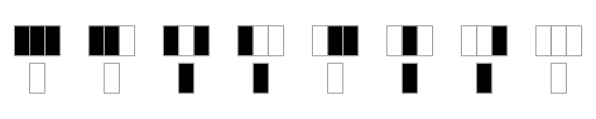

```mathematica
RulePlot[CellularAutomaton[FromDigits[{0, 1, 1, 0, 1, 1, 0}, 2]]]
```

```mathematica
CAP[existingResults]
```

{-Graphics-151,-Graphics-187,-Graphics-189,-Graphics-195,-Graphics-221,-Graphics-635,-Graphics-889,-Graphics-125231,-Graphics-595703,-Graphics-610999,-Graphics-14871103,-Graphics-16537415,-Graphics-256296063,-Graphics-22503642597,-Graphics-222678959859,-Graphics-10495070598767,-Graphics-360759087837221,-Graphics-2197520782601119,-Graphics-11221488970893447375,-Graphics-142082121178470981231}

```mathematica
CAP[{1651650254029552365}]
```

{-Graphics-1651650254029552365}